# 1st, 2nd and 3rd order Differential Equations

```mathematica
Differential equations are powerful mathematical tools that find application in various management contexts,particularly in modeling dynamic systems and decision-making processes.
First-order differential equations are often employed to model simple growth or decay phenomena,such as population growth or depreciation of assets,which are fundamental in managerial economics and finance. 
Second-order differential equations extend this modeling capability to include dynamics with inertia or oscillatory behavior,relevant in supply chain management,project scheduling,and resource allocation.
Third-order differential equations,though less common in management applications,can represent even more intricate dynamics,such as those encountered in complex organizational structures or strategic decision-making processes involving multiple interacting factors.By utilizing these differential equation models,managers can gain deeper insights into system behavior,optimize processes,and make informed decisions to achieve organizational objectives effectively.Thus,understanding and leveraging differential equations in management provide valuable analytical tools for tackling dynamic challenges and enhancing managerial effectiveness.
```

```mathematica
DSolve[y'[x]+y[x]==2Sin[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]-Cos[x]+Sin[x]}}

```mathematica
DSolve[y'[x]-3(1-4(x^2))==0,y[x],x]
```

{{y[x]→3 x-4 x^3+C[1]}}

```mathematica
DSolve[{Y'[X]+Y[X]==X,Y[0]==1},Y[X],X]
```

{{Y[X]→ⅇ^-X (2-ⅇ^X+ⅇ^X X)}}

```mathematica
DSolve[{Y'[X]-3(1-4(X^2))==0,Y[0]==1},Y[X],X]
```

{{Y[X]→1+3 X-4 X^3}}

```mathematica
DSolve[{Y'[X]+Y[X]==2Sin[X],Y[0]==1},Y[X],X]
```

{{Y[X]→-ⅇ^-X (-2+ⅇ^X Cos[X]-ⅇ^X Sin[X])}}

```mathematica
ClearAll
```

ClearAll

```mathematica
DSolve[2x*y[x]*y'[x]-4(x^2)-3(y[x])^2==0,y[x],x]
```

{{y[x]→-x √(-4+x C[1])},{y[x]→x √(-4+x C[1])}}

```mathematica
s=DSolve[2x*y[x]*y'[x]-4(x^2)-3(y[x])^2==0,y[x],x]
```

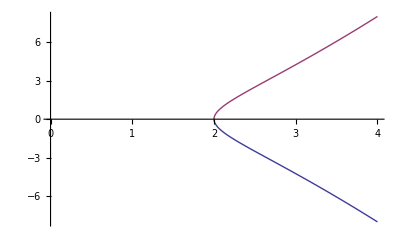

```mathematica
Plot[Evaluate[y[x]/.s/.C[1]->2],{x,0,4}]
```

Plotting of 2nd order differential equation

```mathematica
sol=DSolve[5(x^2)*y''[x]-4x*y'[x]+2y[x]==0,y[x],x]
```

{{y[x]→x^(√(2/5) (-(√(41/10))/2+9/(2 √10))) C[1]+x^(√(2/5) ((√(41/10))/2+9/(2 √10))) C[2]}}

```mathematica
sol=DSolve[5(x^2)*y''[x]-4x*y'[x]+2y[x]==0,y[x],x]
```

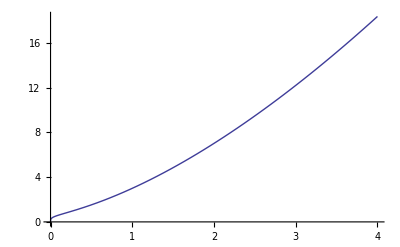

```mathematica
Plot[Evaluate[y[x]/.sol/.C[1]->1/.C[2]->2],{x,0,4}]
```

```mathematica
sol=DSolve[5(x^2)*y''[x]-4x*y'[x]+2y[x]==0,y[x],x]
```

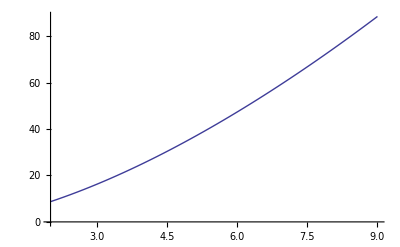

```mathematica
Plot[Evaluate[y[x]/.sol/.C[1]->0/.C[2]->3],{x,2,9}]
```

```mathematica
a=DSolve[{5(x^2)*y''[x]-4x*y'[x]+2y[x]==0,y[1]==1},y[x],x]
```

{{y[x]→x^(√(2/5) ((√(41/10))/2+9/(2 √10)))+x^(√(2/5) (-(√(41/10))/2+9/(2 √10))) C[1]-x^(√(2/5) ((√(41/10))/2+9/(2 √10))) C[1]}}

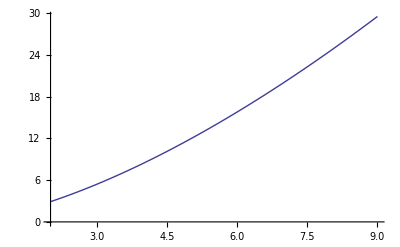

```mathematica
Plot[Evaluate[y[x]/.a/.C[1]->0],{x,2,9}]
```

{{y[x]→x^(√(2/5) (-(√(41/10))/2+9/(2 √10))) C[1]+x^(√(2/5) ((√(41/10))/2+9/(2 √10))) C[2]}}

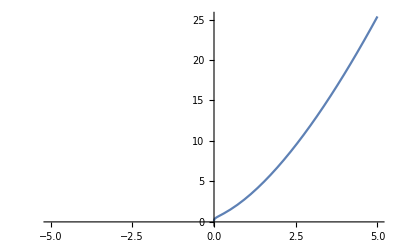

```mathematica
eqn:=5(x)^2*y''[x]-4x*y'[x]+2y[x];
s=DSolve[eqn==0,y[x],x]
Plot[Evaluate[y[x]/.s/.{C[1]->1,C[2]->2}],{x,-5,5}]
```

```mathematica
ClearAll
```

ClearAll

{{y[x]→x^(√(2/5) ((√(41/10))/2+9/(2 √10)))+x^(√(2/5) (-(√(41/10))/2+9/(2 √10))) C[1]-x^(√(2/5) ((√(41/10))/2+9/(2 √10))) C[1]}}

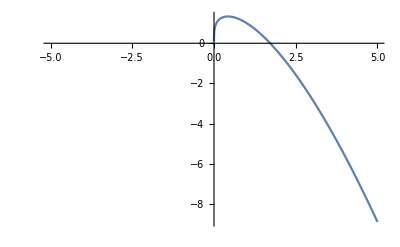

```mathematica
eqn:=5(x)^2*y''[x]-4x*y'[x]+2y[x];
s=DSolve[{eqn==0,y[1]==1},y[x],x]
Plot[Evaluate[y[x]/.s/.C[1]->2],{x,-5,5}]
```

{{y[x]→1/82 (41 x^(√(2/5) (-(√(41/10))/2+9/(2 √10)))-11 √41 x^(√(2/5) (-(√(41/10))/2+9/(2 √10)))+41 x^(√(2/5) ((√(41/10))/2+9/(2 √10)))+11 √41 x^(√(2/5) ((√(41/10))/2+9/(2 √10))))}}

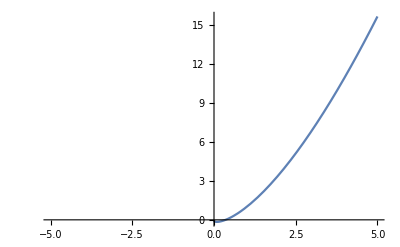

```mathematica
s=DSolve[{eqn==0,y[1]==1,y'[1]==2},y[x],x]
Plot[s[[1,1,2]],{x,-5,5}]
```

{{y[x]→x^(√(2/5) ((√(41/10))/2+9/(2 √10)))+x^(√(2/5) (-(√(41/10))/2+9/(2 √10))) C[1]-x^(√(2/5) ((√(41/10))/2+9/(2 √10))) C[1]}}

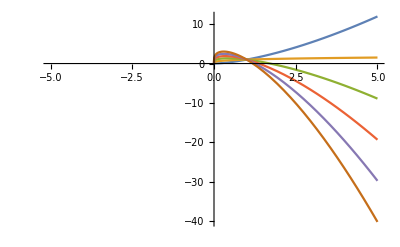

```mathematica
s=DSolve[{eqn==0,y[1]==1},y[x],x]
Plot[Evaluate[y[x]/.s/.C[1]->Range[0,5]],{x,-5,5}]
```

Plotting of 3rd order differential equation

{{y[x]→ⅇ^(-3 x) C[3]+C[1] Cos[2 x]+C[2] Sin[2 x]}}

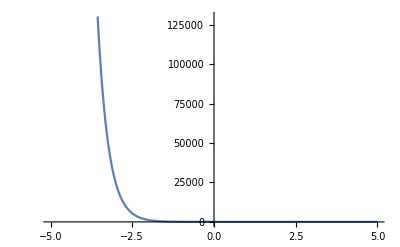

```mathematica
eqn:=y'''[x]+3y''[x]+4y'[x]+12y[x];
s=DSolve[eqn==0,y[x],x]
Plot[Evaluate[y[x]/.s/.{C[1]->1,C[2]->2,C[3]->3}],{x,-5,5}]
```

{{y[x]→ⅇ^(-3 x) (-C[1]+ⅇ^(3 x) C[1] Cos[2 x]+ⅇ^(3 x) C[2] Sin[2 x])}}

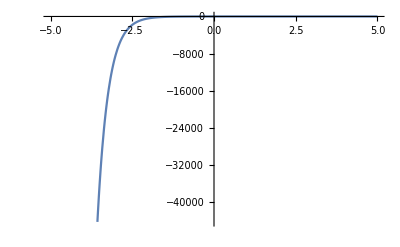

```mathematica
s=DSolve[{eqn==0,y[0]==0},y[x],x]
Plot[Evaluate[y[x]/.s/.{C[1]->1,C[2]->2}],{x,-5,5}]
```

{{y[x]→1/2 ⅇ^(-3 x) C[1] (-2+2 ⅇ^(3 x) Cos[2 x]-3 ⅇ^(3 x) Sin[2 x])}}

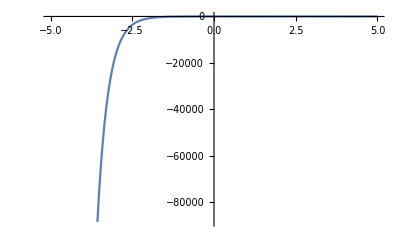

```mathematica
s=DSolve[{eqn==0,y[0]==0,y'[0]==0},y[x],x]
Plot[Evaluate[y[x]/.s/.C[1]->2],{x,-5,5}]
```

{{y[x]→-1/26 ⅇ^(-3 x) (-2+2 ⅇ^(3 x) Cos[2 x]-3 ⅇ^(3 x) Sin[2 x])}}

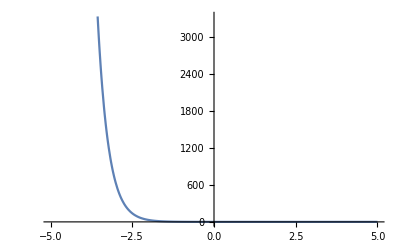

```mathematica
s=DSolve[{eqn==0,y[0]==0,y'[0]==0,y''[0]==1},y[x],x]
Plot[-1/26 ⅇ^(-3 x) (-2+2 ⅇ^(3 x) Cos[2 x]-3 ⅇ^(3 x) Sin[2 x]),{x,-5,5}]
```

{{y[x]→-1/26 a ⅇ^(-3 x) (-2+2 ⅇ^(3 x) Cos[2 x]-3 ⅇ^(3 x) Sin[2 x])}}

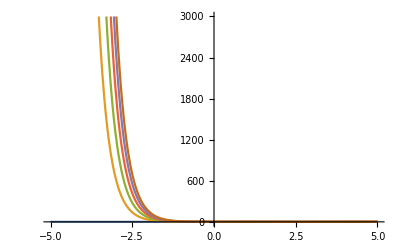

```mathematica
s=DSolve[{eqn==0,y[0]==0,y'[0]==0,y''[0]==a},y[x],x]
Plot[Evaluate[y[x]/.s/.a->Range[0,5]],{x,-5,5}]
```